```mathematica
(*Mathematica*)
```

```mathematica
(*generalized symmetrical matrices as root powers of 2 in SL(2,C) for "a" element of the complex plane ( generalize from "a" in the integers)*)
```

```mathematica
m[1]={{a,1},{a-1,1}}
m[2]={{a,Sqrt[a-1]},{Sqrt[a-1],1}}
m[3]={{a,(a-1)^(1/4)},{(a-1)^(3/4),1}}
m[4]={{a,(a-1)^(1/8)},{(a-1)^(7/8),1}}
```

{{a,1},{-1+a,1}}

{{a,√(-1+a)},{√(-1+a),1}}

{{a,(-1+a)^(1/4)},{(-1+a)^(3/4),1}}

{{a,(-1+a)^(1/8)},{(-1+a)^(7/8),1}}

```mathematica
(*eneralized matrix form on root powers of two*)
```

```mathematica
m[n_]=If[n>4,{{a,(a-1)^(1/2^(n-1))},{(a-1)^((2^(n-1)-1)/2^(n-1)),1}},Nothing]
```

If[n>4,{{a,(a-1)^(1/2^(n-1))},{(a-1)^((2^(n-1)-1)/2^(n-1)),1}},Nothing]

```mathematica
(* sequence of Sl[2,C] matrices to n=10*)
```

```mathematica
Table[Tr[m[i]],{i,10}]
```

{1+a,1+a,1+a,1+a,1+a,1+a,1+a,1+a,1+a,1+a}

```mathematica
Table[Det[m[i]],{i,10}]
```

{1,1,1,1,1,1,1,1,1,1}

```mathematica
Table[CharacteristicPolynomial[m[i],x],{i,10}]
```

{1-x-a x+x^2,1-x-a x+x^2,1-x-a x+x^2,1-x-a x+x^2,1-x-a x+x^2,1-x-a x+x^2,1-x-a x+x^2,1-x-a x+x^2,1-x-a x+x^2,1-x-a x+x^2}

```mathematica
(* Casimir invariant changes : gets larger*)
```

```mathematica
Sum[m[i].m[i],{i,10}]
```

{{-10+10 a+10 a^2,1+(-1+a)^(1/512)+(-1+a)^(1/256)+(-1+a)^(1/128)+(-1+a)^(1/64)+(-1+a)^(1/32)+(-1+a)^(1/16)+(-1+a)^(1/8)+(-1+a)^(1/4)+√(-1+a)+a+(-1+a)^(1/512) a+(-1+a)^(1/256) a+(-1+a)^(1/128) a+(-1+a)^(1/64) a+(-1+a)^(1/32) a+(-1+a)^(1/16) a+(-1+a)^(1/8) a+(-1+a)^(1/4) a+√(-1+a) a},{-1+√(-1+a)+(-1+a)^(3/4)+(-1+a)^(7/8)+(-1+a)^(15/16)+(-1+a)^(31/32)+(-1+a)^(63/64)+(-1+a)^(127/128)+(-1+a)^(255/256)+(-1+a)^(511/512)+a+√(-1+a) a+(-1+a)^(3/4) a+(-1+a)^(7/8) a+(-1+a)^(15/16) a+(-1+a)^(31/32) a+(-1+a)^(63/64) a+(-1+a)^(127/128) a+(-1+a)^(255/256) a+(-1+a)^(511/512) a+(-1+a) a,10 a}}

```mathematica
(* the quadratic roots remain the same: Lamda*)
```

```mathematica
Table[Reduce[CharacteristicPolynomial[m[i],x]==0,x],{i,10}]
```

{x==1/2 (1+a-√(-3+2 a+a^2))||x==1/2 (1+a+√(-3+2 a+a^2)),x==1/2 (1+a-√(-3+2 a+a^2))||x==1/2 (1+a+√(-3+2 a+a^2)),x==1/2 (1+a-√(-3+2 a+a^2))||x==1/2 (1+a+√(-3+2 a+a^2)),x==1/2 (1+a-√(-3+2 a+a^2))||x==1/2 (1+a+√(-3+2 a+a^2)),x==1/2 (1+a-√(-3+2 a+a^2))||x==1/2 (1+a+√(-3+2 a+a^2)),x==1/2 (1+a-√(-3+2 a+a^2))||x==1/2 (1+a+√(-3+2 a+a^2)),x==1/2 (1+a-√(-3+2 a+a^2))||x==1/2 (1+a+√(-3+2 a+a^2)),x==1/2 (1+a-√(-3+2 a+a^2))||x==1/2 (1+a+√(-3+2 a+a^2)),x==1/2 (1+a-√(-3+2 a+a^2))||x==1/2 (1+a+√(-3+2 a+a^2)),x==1/2 (1+a-√(-3+2 a+a^2))||x==1/2 (1+a+√(-3+2 a+a^2))}

```mathematica
(*Positive mu*)
```

```mathematica
mu[n_]:=(1/2 (1+a+√(-3+2 a+a^2))-1)/m[n][[2,1]]
```

```mathematica
Table[mu[n],{n,10}]
```

{(-1+1/2 (1+a+√(-3+2 a+a^2)))/(-1+a),(-1+1/2 (1+a+√(-3+2 a+a^2)))/(√(-1+a)),(-1+1/2 (1+a+√(-3+2 a+a^2)))/(-1+a)^(3/4),(-1+1/2 (1+a+√(-3+2 a+a^2)))/(-1+a)^(7/8),(-1+1/2 (1+a+√(-3+2 a+a^2)))/(-1+a)^(15/16),(-1+1/2 (1+a+√(-3+2 a+a^2)))/(-1+a)^(31/32),(-1+1/2 (1+a+√(-3+2 a+a^2)))/(-1+a)^(63/64),(-1+1/2 (1+a+√(-3+2 a+a^2)))/(-1+a)^(127/128),(-1+1/2 (1+a+√(-3+2 a+a^2)))/(-1+a)^(255/256),(-1+1/2 (1+a+√(-3+2 a+a^2)))/(-1+a)^(511/512)}

```mathematica
(*mu Limit*)
```

```mathematica
Limit[(-1+1/2 (1+a+√(-3+2 a+a^2)))/((-1+a)^((2^(n-1)-1)/2^(n-1))),n->Infinity]
```

(-1+a+√(-3+2 a+a^2))/(2 (-1+a))

```mathematica
(*Limit[m[n],n->Infinity]=m[1]*)
```

```mathematica
Limit[{{a,(a-1)^(1/2^(n-1))},{(a-1)^((2^(n-1)-1)/2^(n-1)),1}},n->Infinity]
```

{{a,1},{-1+a,1}}

```mathematica
(*Bubbling irrationality in SL(2,R)*)
```

```mathematica
MatrixForm[Table[N[{1/2 (1+a+√(-3+2 a+a^2)),mu[n]}],{n,10},{a,2,11}]]
```

((2.61803
1.61803) | (3.73205
1.36603) | (4.79129
1.26376) | (5.82843
1.20711) | (6.8541
1.17082) | (7.87298
1.1455) | (8.88748
1.12678) | (9.89898
1.11237) | (10.9083
1.10093) | (11.9161
1.09161)
(2.61803
1.61803) | (3.73205
1.93185) | (4.79129
2.1889) | (5.82843
2.41421) | (6.8541
2.61803) | (7.87298
2.80588) | (8.88748
2.98119) | (9.89898
3.14626) | (10.9083
3.30278) | (11.9161
3.45197)
(2.61803
1.61803) | (3.73205
1.62449) | (4.79129
1.66321) | (5.82843
1.70711) | (6.8541
1.75078) | (7.87298
1.7928) | (8.88748
1.8328) | (9.89898
1.87078) | (10.9083
1.90686) | (11.9161
1.94118)
(2.61803
1.61803) | (3.73205
1.48966) | (4.79129
1.44979) | (5.82843
1.4355) | (6.8541
1.43173) | (7.87298
1.43306) | (8.88748
1.43707) | (9.89898
1.44257) | (10.9083
1.4489) | (11.9161
1.45568)
(2.61803
1.61803) | (3.73205
1.4265) | (4.79129
1.35359) | (5.82843
1.31636) | (6.8541
1.29472) | (7.87298
1.28123) | (8.88748
1.2725) | (9.89898
1.26676) | (10.9083
1.26298) | (11.9161
1.26057)
(2.61803
1.61803) | (3.73205
1.39594) | (4.79129
1.3079) | (5.82843
1.26055) | (6.8541
1.23121) | (7.87298
1.21147) | (8.88748
1.19743) | (9.89898
1.18706) | (10.9083
1.17917) | (11.9161
1.17305)
(2.61803
1.61803) | (3.73205
1.3809) | (4.79129
1.28564) | (5.82843
1.23354) | (6.8541
1.20064) | (7.87298
1.17802) | (8.88748
1.16157) | (9.89898
1.14911) | (10.9083
1.13938) | (11.9161
1.1316)
(2.61803
1.61803) | (3.73205
1.37344) | (4.79129
1.27466) | (5.82843
1.22025) | (6.8541
1.18563) | (7.87298
1.16164) | (8.88748
1.14404) | (9.89898
1.13059) | (10.9083
1.11999) | (11.9161
1.11142)
(2.61803
1.61803) | (3.73205
1.36973) | (4.79129
1.2692) | (5.82843
1.21366) | (6.8541
1.1782) | (7.87298
1.15354) | (8.88748
1.13538) | (9.89898
1.12144) | (10.9083
1.11042) | (11.9161
1.10147)
(2.61803
1.61803) | (3.73205
1.36788) | (4.79129
1.26648) | (5.82843
1.21038) | (6.8541
1.17451) | (7.87298
1.14951) | (8.88748
1.13107) | (9.89898
1.1169) | (10.9083
1.10566) | (11.9161
1.09653))

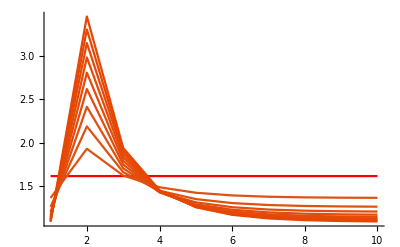

```mathematica
Show[Table[ListLinePlot[Table[mu[n],{n,10}],ColorFunction->Hue,ImageSize->Full,PlotRange->All],{a,2,11}],PlotRange->All]
```

```mathematica
N[1/2 (1+a+√(-3+2 a+a^2))]/.a->1.91
```

{{1.60771,0.549563+0.958148 ⅈ},{0.919349-3.24868 ⅈ,1.60771}}

```mathematica
(-1+1/2 (1+a+√(-3+2 a+a^2)))/(√(-1+a))/.a->1.91
```

{{1.26796,0.909431+0.526784 ⅈ},{1.46554-1.10836 ⅈ,1.26796}}

```mathematica
(*end*)
```